## Another Fourier Problem — SOLVED

## A Fourier Localization Problem with no Ringing

## For Quantum Mechanics, Monday, Mar. 16, 2026

### The Function to Approximate With Cosines

An issue with our first and easiest example of localization (a step-up-and-step-down function that was nonzero only between -L/8 and L/8) appeared at the discontinuities.

It is difficult for a bunch of continuous functions (in this case the sum of any number of cosines) to well-approximate any function with a discontinuity, even if the function is even and vanishes at the edge of the box.

The function when approximated by cosines exhibits ringing.

Here and below, I will frequently specialize to the case L=4 for definiteness. The box then goes from -2 to 2.

Here is a polynomial of degree six, that is concentrated on [-1, 1], and small on [-2, -1] and on  [1, 2]:

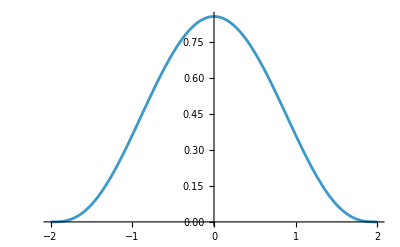

```mathematica
ψ[x_]:=(√3003)/64(1-x^2/4)^3

Plot[ψ[x],{x, -2, 2}]
```

Square this function to get a probability distribution:

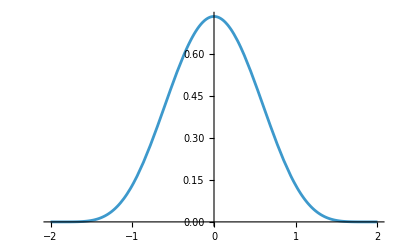

```mathematica
prob[x_]:=ψ[x]^2

Plot[prob[x],{x, -2, 2}]
```

Confirm that the constant out front has been chosen so that the probability of being somewhere in the box is 1:

```mathematica
Integrate[prob[x],{x, -2, 2}]
```

1

### The Coefficients

Again, the only cosines we have to consider are √(2/L)cos (n π x)/L where n is any odd integer. Here are the first three of those functions:

```mathematica
Plot[{c[x,1], c[x,3], c[x,5]},{x, -2, 2}]
```

Apply the powerful mathematics of Fourier analysis for n=1, 3, 5:

```mathematica
L=4;
c[x_,n_]:=Sqrt[2/L]Cos[(n Pi x)/L];
tableOfCoefficients=Table[Integrate[ψ[x]c[x,n], {x, -L/2,L/2}],{n,1,5,2}]
```

{-(288 √6006 (-10+π^2))/π^7,(32 √(2002/3) (-10+9 π^2))/(81 π^7),-(288 √6006 (-2+5 π^2))/(15625 π^7)}

Let’s see what these coefficients are numerically:

```mathematica
N[tableOfCoefficients]
```

{0.963605,0.266354,-0.0223933}

### Assembling the Series — First Term Only

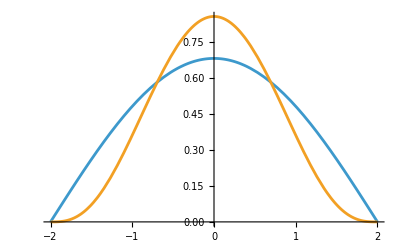

```mathematica
oneTermOnly[x_]:=tableOfCoefficients[[1]]c[x,1]

Plot[{oneTermOnly[x],ψ[x]}, {x, -2, 2}]
```

### Assembling the Series — First Two Terms

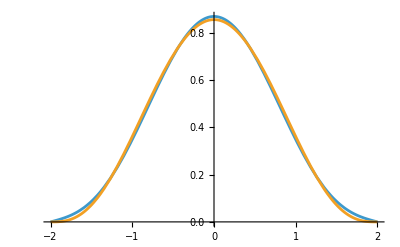

```mathematica
twoTerms[x_]:=tableOfCoefficients[[1]]c[x,1]+tableOfCoefficients[[2]] c[x,3]

Plot[{twoTerms[x],ψ[x]}, {x, -2, 2}]
```

### Assembling the Series — First Three Terms

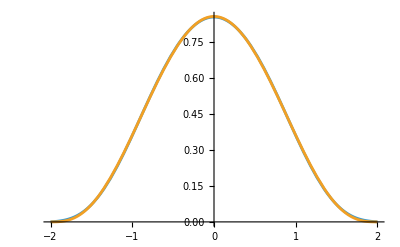

```mathematica
threeTerms[x_]:=tableOfCoefficients[[1]]c[x,1]+tableOfCoefficients[[2]]c[x,3]+tableOfCoefficients[[3]] c[x,5]

Plot[{threeTerms[x],ψ[x]}, {x, -2, 2}]
```

### Probability — Square of the First Three Terms

Let’s square it and see what it looks like, since that gives the probability distribution:

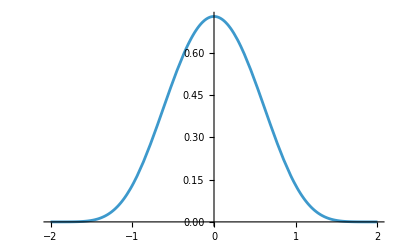

```mathematica
Plot[(threeTerms[x])^2, {x,-2, 2}]
```

### Normalization — Integrate the Square of the First Three Terms

Double-check that your mathematics agrees with mine by doing the integral that should come out very near 1, and would quickly get even closer to 1 if we included more terms:

```mathematica
N[Integrate[(threeTerms[x])^2, {x,-2, 2}]]
```

0.99998

### Conclusion

Is it not remarkable that out of the following three cosines, we were able to make a polynomial of degree 6 that was reasonably localized?

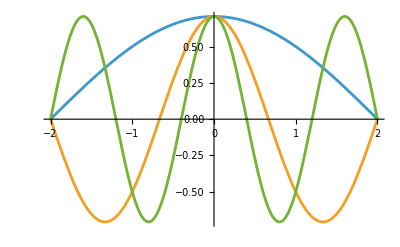

```mathematica
Plot[{c[x,1], c[x,3], c[x,5]},{x, -2, 2}]
```